ENHANCING QED EFFECTS BY TEMPORAL PULSE SHAPING IN LASER - ELECTRON-BEAM COLLISIONS + 
Effect of laser temporal intensity skew on enhancing pair production in laser-electron-beam collisions

Laurence E. Bradley, Master of Science by Research, University of York, Physics, June 2019
L E Bradley et al 2021 New J. Phys. 23 095004
Notebook: Óscar Amaro, December 2022 @ GoLP-EPP

Introduction
In this notebook we (try to) reproduce some results from the paper and thesis.

## Figure 3 (paper)

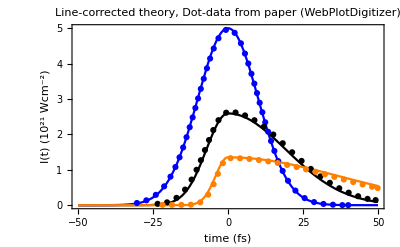

125.331

86.0556

69.7147

```mathematica
Clear[It,t,ℛ,τp,τf,τr,I0,int,int1,int2,dataℛ1,dataℛ052,dataℛ072]

dataℛ1={{-30.357554955318683,0.06162322941545817},{-27.208610937678245,0.13702164016137974},{-24.057382844049172,0.2919058953119622},{-21.27831416856715,0.5322916136047295},{-19.17260747260036,0.8056490311544353},{-17.51644964696007,1.0786848189341134},{-16.159985387524152,1.3517038745292238},{-14.953199814706572,1.630564321670163},{-13.820995298698278,1.921333834779778},{-12.763972737397445,2.2031011670016096},{-11.782001548940386,2.480410567192125},{-10.875272072992814,2.7466382149842685},{-9.968449640464314,3.0161007517928815},{-9.061565236881847,3.28771988127914},{-8.079386002743647,3.5722692711731803},{-7.021965056095979,3.867900413465592},{-5.965101848933884,4.144122221659191},{-4.758212622151049,4.4265898267907176},{-3.1764840980129208,4.716815765227067},{-0.697234701444728,4.952809949046327},{2.222382480031399,4.869623990070146},{4.311744826942913,4.574198060496403},{5.652043936954584,4.284669916127591},{6.767798458015633,4.002979605072819},{7.808407543026007,3.7135579623867327},{8.774416758585701,3.435390705749321},{9.665808398679332,3.1678616658241148},{10.55701412561109,2.893862847865971},{11.448374780177716,2.6252555116019427},{12.414246774117956,2.342312942606887},{13.380551680135113,2.074435713888529},{14.347026563900258,1.812473710800285},{15.462844162641218,1.5329785030066887},{16.72832923419074,1.2472516630874964},{18.218774395852662,0.968146430283432},{20.008917930448135,0.6892252038395741},{22.473415696472756,0.4118626447427758},{25.53918482139666,0.20010463188483385},{28.682728504335273,0.08757139500733047},{31.82799852377694,0.0351146684356749},{34.97415384398937,0.013466408687533793},{38.12059246044848,0.0016768583229147538},{40.068590570480666,0.0014351712124893723}};

dataℛ052={{-21.81781092515711,0.009113384797555746},{-18.671044747412815,0.008722967157637207},{-15.524278569668525,0.008332549517718668},{-12.377353037785483,0.01348765590603307},{-9.228639198345448,0.08087586527784119},{-6.600128091821972,0.29651786967739646},{-4.793501005975017,0.5912242267846404},{-3.3614883510876012,0.8859976011602324},{-1.704538090457362,1.1866101265897049},{0.846915755975914,1.3279893227820558},{3.9935845506354326,1.324209973791552},{7.1398372539326544,1.3059506453939953},{10.285744689929288,1.2756760149352697},{13.431439653740924,1.2380073524389},{16.57689558634445,1.1920204039001838},{19.722103634732136,1.1374070846508832},{22.867161181988806,1.0775563260415861},{26.012068228114444,1.0124681280722925},{29.156860185139877,0.9433748294159416},{32.30158131810364,0.8718168534137103},{35.446267039036584,0.799026538738536},{38.5909350539541,0.7256200547268934},{41.735647333910165,0.6537539940564265},{44.88046584995871,0.5855849494047813},{48.02535519006892,0.5198805820990167},{49.897401133723065,0.4838333479643513}};

dataℛ072={{-23.465293688544428,0.03796976342147573},{-20.31731464874415,0.0797869453297686},{-17.166901031824203,0.20632741100271978},{-14.313087128316418,0.4405172216598192},{-12.132184482078529,0.7233638657125345},{-10.475936798410004,0.9995267128747987},{-9.04460582511608,1.2705775677962858},{-7.687749598763901,1.5572370720775064},{-6.330976000483645,1.8410211194551986},{-4.8993413690253504,2.1226392784971515},{-3.1680751026915885,2.4021189594772294},{-0.6146184335145506,2.6131963871526187},{2.5323248043839044,2.618967662877402},{5.676727229070195,2.536318638818706},{8.819615789438416,2.4009871364918034},{11.9611055745888,2.2169782565837517},{15.101541851821935,1.9963073011557197},{18.24125218242304,1.750373402932409},{21.38069692279288,1.4951969646620435},{24.520451518432523,1.2508034897799085},{27.615773753686952,1.024561779251676},{30.801439161999014,0.8134666796109018},{33.94300862421875,0.6322305617169661},{37.08537485713222,0.4787220639641907},{40.22856441976252,0.35386544035728296},{43.37246222300945,0.2536555902091848},{46.51706826687301,0.1780925135198963},{49.203334625081325,0.14393141267740006}};

(* from the figure in the paper it seems that insensity is scaled with ℛ^2 instead of ℛ . also, τf and τr don't seem to follow eq 1 and eq 2. It would seem that τr->ℛ 20,τf->20/ℛ^2, but for the orange curve τr does not follow this *)
Show[{Plot[{(5 Exp[-2 t^2/τp^2]/.{τp->20}),(5 ℛ^2 Piecewise[{{Exp[-2 t^2/τr^2],t<0},{Exp[-2 t^2/τf^2],t>0}}]//.{ℛ->0.72,τp->20,τr->ℛ τp,τf->τp/ℛ^2}),(5 ℛ^2 Piecewise[{{Exp[-2 t^2/τr^2],t<0},{Exp[-2 t^2/τf^2],t>0}}]//.{ℛ->0.52,τp->20,τr->0.8ℛ τp,τf->τp/ℛ^2})},{t,-50,+50},PlotRange->All,PlotStyle->{Blue,Black,Orange},Frame->True,FrameLabel->{"time (fs)","I(t) (10^21 Wcm^-2)"},PlotLabel->"Line-corrected theory, Dot-data from paper (WebPlotDigitizer)"],ListPlot[{dataℛ1,dataℛ072,dataℛ052},PlotStyle->{Blue,Black,Orange}]}]

(* energy does not seem to be kept constant between pulses *)
τp=20;
NIntegrate[5 Exp[-2 t^2/τp^2],{t,-∞,+∞}]

ℛ=0.72;τr=ℛ τp;τf=τp/ℛ^2;
5 ℛ^2 (NIntegrate[Exp[-2 t^2/τr^2],{t,-∞,0}]+NIntegrate[Exp[-2 t^2/τf^2],{t,0,∞}])

ℛ=0.52;τr=0.8ℛ τp;τf=τp/ℛ^2;
5 ℛ^2 (NIntegrate[Exp[-2 t^2/τr^2],{t,-∞,0}]+NIntegrate[Exp[-2 t^2/τf^2],{t,0,∞}])
```

-(2 γ0 δ)/(√π (1+δ)^2 τr)

Piecewise[{{2931/(1+0.776826 τp (1+Erf[t/τr])), t<0}, {2931/(1+0.776826 τp (1+Erf[t/τf])), t≥0}, {0, True}}]

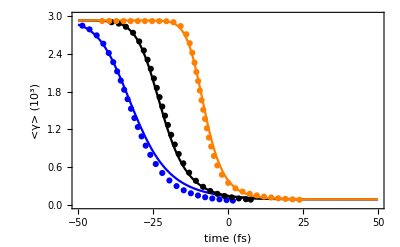

```mathematica
Clear[me,c,α,λc,ϵ0]
Clear[δ,τrf,γ0,t,τp,τr,τf,τrf,γavg,Ecrit,γ,E0,I0,I1,ℛ,dataℛ1,dataℛ072,dataℛ052]

(* data from the paper, taken with WebPlotDigitizer *)
dataℛ1={{-48.54359279470809,2.848792281131093},{-46.16018892127147,2.789944717581904},{-43.775324907144004,2.6942468533477477},{-41.559073613651464,2.561604833829775},{-39.73908070876641,2.4141492814086374},{-38.25930437039602,2.2682939417859966},{-36.94960492471627,2.1224464891354207},{-35.75326652509319,1.9760099748019755},{-34.61364034387569,1.8300788417096414},{-33.47387788286036,1.6807083472200435},{-32.333992770027,1.5282424274729083},{-31.194284820930804,1.380247677542216},{-30.054794919511103,1.2377559058471457},{-28.801690821986057,1.0894643214818451},{-27.43524735928125,0.9423089699307972},{-25.89875623619742,0.7958834818719018},{-24.078825579750358,0.6499989244045845},{-21.918894234931464,0.507962378768581},{-19.533089241247687,0.3885165429818911},{-17.14847182865912,0.29904228508564046},{-14.76479539562687,0.23331599874192444},{-12.381819830126219,0.18527785672699215},{-9.999337467703363,0.14968692738787093},{-7.617186070503763,0.12244873287067559},{-5.235326701442332,0.10258059849047374},{-2.853713933919792,0.08893607044817742},{-0.47219201959579493,0.07758445000405656},{1.625752320809255,0.06917569749291852}};
dataℛ072={{-38.79466819944804,2.9026155005631162},{-36.41275691427315,2.881437133269671},{-34.02968400605978,2.8309423045424076},{-31.644819991932316,2.735244440308252},{-29.5984711018597,2.5982066347929473},{-28.062077645964308,2.4542460224020908},{-26.80903260301831,2.3074448279756052},{-25.726147272729534,2.1627416894280493},{-24.69964240901529,2.0101713452858414},{-23.72993025826394,1.8601378637757036},{-22.817025962675253,1.7130233961639987},{-21.90400242226349,1.5628994873296882},{-20.991183301548432,1.4179346205912733},{-20.02155064734582,1.2699074332295393},{-18.93823376436397,1.1143129835906485},{-17.741574487762414,0.9597783365127377},{-16.431698497799125,0.8094753475066159},{-14.895134692156468,0.6612155333691803},{-12.961711204569504,0.5125941115471835},{-10.688919734142907,0.38378860742496457},{-8.304055720015434,0.28809074319080885},{-5.9203792869831915,0.22236445684709238},{-3.5375010641952542,0.17678300154449111},{-1.1550602346631678,0.14224025853596478},{1.2268666253457496,0.12066882136854673},{3.6086156726661045,0.10358493192898655},{5.990189503103537,0.09092307857162307},{7.577849147605605,0.08390126198939374}};
dataℛ052={{-41.970214621448505,2.922391402723014},{-39.58914697311721,2.9225043202697716},{-37.20804038770084,2.921634563131597},{-34.82697273936955,2.921747480678355},{-32.44589211200989,2.9215328399968024},{-30.064811484650242,2.9213181993152495},{-27.683730857290584,2.9211035586336966},{-25.302650229930933,2.920888917952144},{-22.92156960257128,2.920674277270591},{-20.540385142984718,2.9178391707625515},{-18.15873343837709,2.9032119680353228},{-15.775238711741927,2.8420714968879577},{-13.899222371720896,2.711493730991922},{-12.75976426892069,2.569804476956213},{-11.903386886609887,2.418518752425963},{-11.160100645561414,2.259832243965017},{-10.530656058090344,2.1126860061254473},{-9.958008347687112,1.9681817225161977},{-9.385115333647818,1.817486588391874},{-8.812086039810715,1.6633520928702863},{-8.239165769811862,1.5119690864665094},{-7.666490803449065,1.3667769305778075},{-7.037000789378723,1.21848423893915},{-6.350832007398651,1.0705303729478008},{-5.6082141863108745,0.928713113244862},{-4.69516117268887,0.7778453742670957},{-3.5553678766485746,0.6276966808350868},{-2.018812382008747,0.4796466156313479},{0.08392689818717258,0.35022557014863276},{2.468414520492118,0.26402689453549044},{4.8515393448189315,0.21222183289498364},{7.2340152177276025,0.1767946826700184},{9.616082251242844,0.15168561663684343},{11.997922151761742,0.13230881959910734},{14.379560877341007,0.11800917510018971},{16.76109577069336,0.1063299964277582},{19.142552789875538,0.0966161671251915},{21.52393842440172,0.08870390807833495},{23.848580395876354,0.08209061452572275}};

(* the derivative of γavg at t->0 is discontinuous (has τr and τf as pre-factors) *)
D[γ0/(1+δ (1+Erf[t/τr])),t]/.{t->0}

me = 9.1 10^-31;(*[Kg]*)
c=3 10^8;(*[m/s]*)
α=1/137//N;(*[]*)
λc=3.86 10^-13;(*[m] defined after eq 4 in paper *)
τrf=0.5τp;
ϵ0=8.854 10^-12;(*[F/m]*)
Ecrit=1.38 10^18;(*[V/m] defined in §1 Introduction *)
δ= 2√π τrf γ0 α c E0^2/(3λc Ecrit^2) 10^-15 4;(* defined after eq 7 in paper. Got to multiply by 10^-15 because τrf in fs *)

I0=5 10^21 10^4;(*[W/m^2]*)
E0=Sqrt[(2 I0)/(c ϵ0)];(*[V/m] *)

γ0=2931;(*[] in text *)
γavg=Piecewise[{{γ0/(1+δ (1+Erf[t/τr])),t<0},{γ0/(1+δ (1+Erf[t/τf])),t>=0}}]
(* also, the 3 curves don't have the same t0... so t->tt+X. Is τr->ℛ τp,τf->τr? Derivative of <γ> seems continuous in the plot, so τr=τf must hold  *)
Show[{Plot[{(10^-3 γavg//.{ℛ->1,I1->I0 ℛ^2,τp->20,τr->ℛ τp,τf->τr,t->tt+5}),(10^-3 γavg//.{ℛ->0.72,I1->I0 ℛ^2,τp-> 20,τr->ℛ τp,τf->τr,t->tt+3}),(10^-3 γavg//.{ℛ->0.52,I1->I0 ℛ^2,τp->20,τr->ℛ τp,τf->τr,t->tt-6})},{tt,-50,+50},Frame->True,FrameLabel->{"time (fs)","<γ> (10^3)"},PlotRange->{0,3},PlotStyle->{Blue,Black,Orange}],ListPlot[{dataℛ1,dataℛ072,dataℛ052},PlotStyle->{Blue,Black,Orange}]}]
```

```mathematica
Clear[me,c,α,λc,g,χe,P]
Clear[γ0]


g[χe_]:=(1+4.8(1+χe)Log[1+1.7χe]+2.44χe^2)^(-2/3)
P[χe_]:=10^-15 2/3(α c)/λc (me c^2)/(me c^2)χe^2 g[χe];(*[] adimensional, multiplied by fs/s and mc^2, equation 4 *)

γ0=2931;
```

## Figure 8 (paper): Gaunt factor

§2.2 Modified-classical emission equations

```mathematica
Clear[χe,χγ,t,y,g,F,χelst,glst, lst1,lst2,lst3]

F[χe_?NumericQ,χγ_?NumericQ]:=F[χe,χγ]=(4χγ^2)/χe^2(4χγ)/(3χe(χe-2χγ))BesselK[2/3,(4χγ)/(3χe(χe-2χγ))]+(1-(2χγ)/χe)(4χγ)/(3χe(χe-2χγ))NIntegrate[BesselK[5/3,t],{t,(4χγ)/(3χe(χe-2χγ)),∞}]
g[χe_?NumericQ]:=g[χe]=(3√3)/(2π χe^2)NIntegrate[F[χe,χγ],{χγ,0,χe/2}]


χe=10^ParallelTable[x,{x,-2,2,0.2}];
glst=ParallelTable[g[χe[[i]]],{i,1,Length[χe]}];
lst1=1-(55√3)/16 χe+4.8χe^2;
lst2=0.5564χe^(-4/3);
lst3=(1+4.8(1+χe)Log[1+1.7χe]+2.44χe^2)^(-2/3);
```

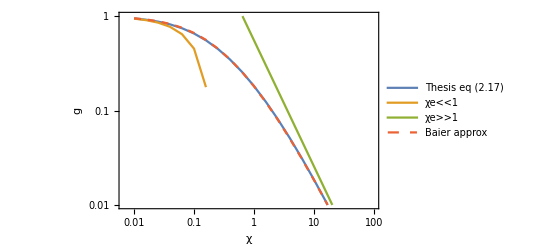

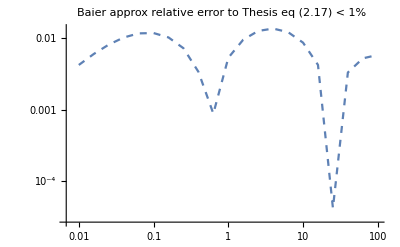

```mathematica
ListLogLogPlot[{Transpose[{χe,glst}],Transpose[{χe,lst1}],Transpose[{χe,lst2}],Transpose[{χe,lst3}]},PlotRange->{10^-2,10^0},PlotLegends->{"Thesis eq (2.17)","χe<<1","χe>>1","Baier approx"},PlotStyle->{Default,Default,Default,Dashed},Joined->True,Frame->True,FrameLabel->{"χ","g"}]

ListLogLogPlot[Transpose[{χe,Abs[glst-lst3]/Abs[glst]}],PlotLabel->"Baier approx relative error to Thesis eq (2.17) < 1%",PlotStyle->{Default,Default,Default,Dashed},Joined->True]
```

## Figure 1.4 (thesis) Rate of photon emission

(1.19111×10^-8 χe^(2/3))/λc

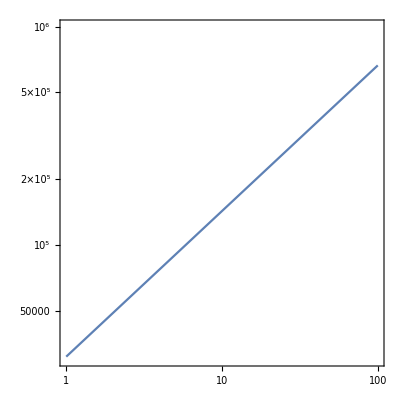

```mathematica
Clear[χe,h,α,c,λc,γ,dNγdt,λγ,f]
h=5.298 χe^(-1/3);(*eq 1.5 *)
α=1/137;
λγ=(√3 α c)/λc χe/γ h;
f=(γ λγ)/c 10^-6.75(*[μm]???*)
λc=3.86 10^-13;(*[m] defined after eq 4 in paper *)
LogLogPlot[f,{χe,1,100},PlotRange->{3 10^4,10^6},AspectRatio->1,Frame->True]
```

## Figure 3.4 (thesis)

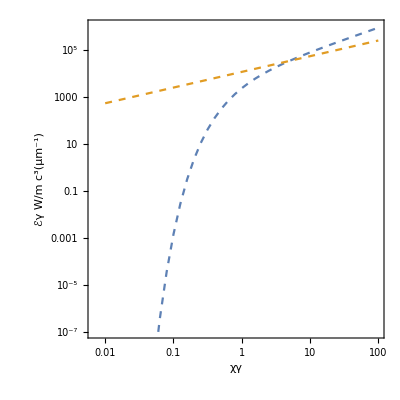

```mathematica
Clear[χγ,Tm,Tp,T,x,Wpm,ℰγ]
Clear[x,me,m,ℏ,α,c,τc,e]

(* see table 1.1 definition of fundamental constants*)
c=2.998 10^8;(*[m/s]*)
me=m=9.11 10^-31;(*[Kg]*)
e=1.6 10^-19;(*[C]*)
ℏ=1.06 10^-34;(*[Js]*)
α=1/137;(*[]*)
τc=1.29 10^-21;(*[s]*)

Wpm=α/τc(me c^2)/(ℏ ω) χγ T[χγ];(*[1/s] eq 3.5*)
ℰγ=ℏ ω;

χγ=10^ParallelTable[x,{x,-2,2,0.1}];
(* aux function T *)
Tm=(3√3)/(8√2)Exp[-4/(3χγ)];
Tp=0.6 χγ^(-1/3);

(* function to plot does not depend on ω directly *)
fm=ℰγ/(m c^3) α/τc(me c^2)/(ℏ ω) χγ Tm 10^-6;(*[μm]*)
fp=ℰγ/(m c^3) α/τc(me c^2)/(ℏ ω) χγ Tp 10^-6;(*[μm]*)

ListLogLogPlot[{Transpose[{χγ,fm}],Transpose[{χγ,fp}]},Joined->True,AspectRatio->1,Frame->True,PlotRange->{10^-7,10^6},FrameLabel->{"χγ","ℰγ W/m c^3(μm^-1)"},PlotStyle->{Dashed,Dashed}]
```

## Figure 3.8 (thesis)

The theoretical model of eq 3.11 has a factor of 2 missing in its argument...

0.470588

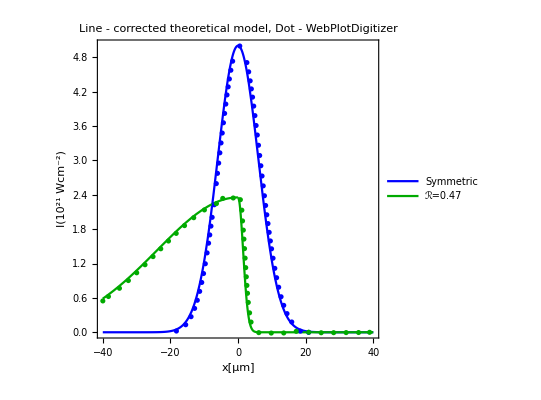

0.

```mathematica
Clear[It,t,ℛ,τp,τf,I0,int,int1,int2,c,I1,datasym,dataskew,datasym]
τp=40;
τr=10;
τf=160;
ℛ=2τp/(τr+τf)//N(*[], = 0.47058823529411764*)

c=3 10^8;(*[m/s]*)
I0=5 ;(*[10^21 W cm^-2]*)
I1=I0 ℛ;

(* data extracted from figure 3.8 using WebPlotDigitizer *)
dataskew={{-38.327826580639375,0.6238761301945832},{-39.98781373434649,0.5467647130081081},{-35.067963228651884,0.7673988839843311},{-32.432329029172635,0.9023131820712571},{-29.972403776325336,1.037849038835752},{-27.512478523478038,1.1784058274380769},{-25.14040774394671,1.320159958518385},{-22.85619143773137,1.4566509323692536},{-20.571975131516012,1.5921587866994278},{-18.287758825300656,1.7252088422278664},{-15.827833572453358,1.8609764343079522},{-13.104344899658145,1.999026138090243},{-9.941583860283032,2.134997029577387},{-6.387471076136777,2.245327460160323},{-4.523891339131254,2.3363551801571143},{-1.4196999486334647,2.3430490045855836},{0.6888074109499343,2.3133764808086057},{1.1280797775298055,2.1303463280669908},{1.3330735486004244,1.9429718389413368},{1.567352144109691,1.7822340224754507},{1.7430610907416337,1.625735352650648},{1.9187700373735908,1.4596512674990763},{2.0944789840055336,1.2935671823475037},{2.2701879306374906,1.1274830971959329},{2.4458968772694334,0.9677892889288735},{2.6216058239013904,0.8176808959885848},{2.797314770533333,0.6803530568173226},{3.031593366042614,0.5206802864988553},{3.4122960837451615,0.3386941419560676},{3.8515684503250327,0.17802995831025026},{6.135784756540389,-0.0064675913455856104},{9.82567263581133,-0.013662569763704724},{13.515560515082285,-0.012337179002471999},{17.20544839435324,0.016375112692387894},{20.89533627362418,0.000761198061339563},{24.585224152895137,-0.00836100671877471},{28.275112032166092,-0.007035615957542873},{31.964999911437033,-0.005710225196310148},{35.65488779070799,-0.004384834435077423},{38.90550330339906,-0.0008208744565862958}};
datasym={{-18.22626069397947,0.02131275679445821},{-15.476415679189458,0.13119661593553467},{-13.895035159501916,0.2717697977445539},{-12.840781479710216,0.4165687384091923},{-12.050091219866431,0.5583973837071392},{-11.347255433338631,0.7136140535396782},{-10.732274120126817,0.8693316895230394},{-10.20514728023096,1.0250177685835142},{-9.678020440335118,1.195614493707855},{-9.150893600439261,1.3853820494857327},{-8.71162123385939,1.5548821715397674},{-7.042386240855862,2.224736465519349},{-8.36020334059549,1.698789629132862},{-8.00878544733159,1.8522825020527263},{-7.65736755406769,2.0057753749725906},{-6.427404927644034,2.594122645268222},{-6.075987034380134,2.773176625726139},{-5.724569141116234,2.9522306061840564},{-5.373151247852334,3.131284586641974},{-5.021733354588434,3.303948290215378},{-4.670315461324535,3.4766119937887825},{-4.318897568060635,3.6556659742466997},{-3.967479674796735,3.818744262493334},{-3.616061781532835,3.9818225507399685},{-3.2646438882689353,4.141705700544346},{-2.9132259950050354,4.282418019695184},{-2.5618081017411356,4.419935200403765},{-2.1225357351612644,4.572394584099097},{-1.5954088952654075,4.73021075545441},{0.5130984643179914,4.995293210917644},{2.6216058239013904,4.706164380214908},{3.148732663797233,4.544466707344558},{3.5880050303771185,4.386997662140996},{3.9394229236410183,4.24653779837325},{4.290840816904918,4.102882796163248},{4.642258710168818,3.9464472401842188},{4.993676603432718,3.7804262688784194},{5.345094496696618,3.608015020688107},{5.6965123899605175,3.4419940493823082},{6.047930283224417,3.2631925243074824},{6.399348176488317,3.084390999232657},{6.750766069752217,2.905589474157831},{7.102183963016117,2.726787949083006},{7.453601856280017,2.5543767008926936},{7.805019749543916,2.381965452702381},{8.156437642807816,2.2127493429543255},{8.507855536071716,2.0499235100907836},{8.859273429335616,1.896683092554011},{9.210691322599516,1.7434426750172385},{9.562109215863416,1.5933973959227226},{9.913527109127315,1.456132670597233},{10.352799475707187,1.2922733485091582},{10.879926315603043,1.1156650295749433},{11.407053155498886,0.9518372644097557},{12.022034468710714,0.7859109638726158},{12.724870255238514,0.6200162202583632},{13.515560515082285,0.469489698089828},{14.481959721558013,0.325629575881063},{15.887631294613612,0.1795841367624087},{18.435411020776883,0.02067136233679001},{20.89533627362418,-0.0023832238977075093}};

(* extra 2 in argument of exponential *)
It[t_]:=Module[{},
Return[I1 Piecewise[{{Exp[-2 t^2/τf^2],t<0},{Exp[-2 t^2/τr^2],t>0}}]]
]

Show[{Plot[{I0 Exp[-2((x 10^-6)/c 10^15)^2/τp^2],It[(x 10^-6)/c 10^15]},{x,-40,+40},PlotRange->{0,5},PlotStyle->{Blue,Green//Darker},Frame->True,FrameLabel->{"x[μm]","I(10^21 Wcm^-2)"},AspectRatio->1,PlotLabel->"Line - corrected theoretical model, Dot - WebPlotDigitizer",PlotLegends->{"Symmetric","ℛ=0.47"}],ListPlot[{datasym,dataskew},PlotStyle->{Blue,Green//Darker}]}]

(* confirm they have the same energy *)
I0 τp √π-1/2 √π(τr+τf)I1//N
```

## Figure 3.9 (thesis): Conserving the energy in the modified pulse

```mathematica
(* since there is only one explicit equation/constraint (conservation of energy between the symmetric and skewed pulse), there is ambiguity regarding ℛ vs τf (you have to fix one to get the other)*)
Clear[It,t,ℛ,τp,τf,τr,I0,int,int1,int2,c,I1]
I0=5 ;(*[10^21 W cm^-2]*)
τp=40;(*[fs]*)
τr={5,10,15,20,25,30,35,40};(*[fs]*)
(* retrieved with WebPlotDigitizer *)
I1={2.1783490443656484,2.3625789155063557,2.591304159820116,2.8685462250281066,3.218563521577445,3.657506702412869,4.23391420911528,5.020582893712704};
ℛ=I1/I0
τf=2τp/ℛ-τr
```

{0.43567,0.472516,0.518261,0.573709,0.643713,0.731501,0.846783,1.00412}

{178.625,159.307,139.362,119.443,99.279,79.3641,59.4752,39.672}